```mathematica
Quit[];
```

```mathematica
ClearAll[assum]
```

```mathematica
assum={x>0&&MD1>0&&mx>0&&Ex>0&&Eb>0&&T>0&&Element[{x,MD1,mx,Ex,Eb,T}, Reals]};
```

```mathematica
sfromθ=mx^2+2 Eb (Ex-√(Ex^2-mx^2)cosθ);
```

```mathematica
(sfromθ/.cosθ-> -1)
```

mx^2+2 Eb (Ex+√(Ex^2-mx^2))

```mathematica
Sint=Collect[ Integrate[(σ0+σ1 s+σ2 s^2)(s-mx^2),{s,(sfromθ/.cosθ-> 1),(sfromθ/.cosθ->- 1)},Assumptions->assum],{σ0,σ1,σ2}]
```

8 Eb^2 Ex √(Ex^2-mx^2) σ0+8/3 Eb^2 √(Ex^2-mx^2) (8 Eb Ex^2-2 Eb mx^2+3 Ex mx^2) σ1+8/3 Eb^2 √(Ex^2-mx^2) (24 Eb^2 Ex^3-12 Eb^2 Ex mx^2+16 Eb Ex^2 mx^2-4 Eb mx^4+3 Ex mx^4) σ2

```mathematica
EbintFermions=Collect[Integrate[Sint/(ⅇ^(Eb/T)+1),{Eb,0,∞},Assumptions->assum],{σ0,σ1,σ2}]
```

12 Ex √(Ex^2-mx^2) T^3 σ0 Zeta[3]+2/45 √(Ex^2-mx^2) T^3 σ1 (28 Ex^2 π^4 T-7 mx^2 π^4 T+270 Ex mx^2 Zeta[3])+2/45 √(Ex^2-mx^2) T^3 σ2 (56 Ex^2 mx^2 π^4 T-14 mx^4 π^4 T+270 Ex mx^4 Zeta[3]+16200 Ex (2 Ex^2-mx^2) T^2 Zeta[5])

```mathematica
EbintBosons=Collect[Integrate[Sint/(ⅇ^(Eb/T)-1),{Eb,0,∞},Assumptions->assum],{σ0,σ1,σ2}]
```

16 Ex √(Ex^2-mx^2) T^3 σ0 Zeta[3]+8/3 √(Ex^2-mx^2) σ1 (2/15 (4 Ex^2-mx^2) π^4 T^4+6 Ex mx^2 T^3 Zeta[3])+8/3 √(Ex^2-mx^2) σ2 (4/15 mx^2 (4 Ex^2-mx^2) π^4 T^4+6 Ex mx^4 T^3 Zeta[3]+288 Ex (2 Ex^2-mx^2) T^5 Zeta[5])

```mathematica
TimeUsed[]
```

28.951

```mathematica
ExintFermions=Collect[Integrate[EbintFermions ⅇ^(-Ex/T),{Ex,mx,∞},Assumptions->assum],{σ0,σ1,σ2}]
```

12 mx^2 T^4 σ0 BesselK[2,mx/T] Zeta[3]+2/15 mx^2 T^4 σ1 (7 mx π^4 T BesselK[1,mx/T]+28 π^4 T^2 BesselK[2,mx/T]+90 mx^2 BesselK[2,mx/T] Zeta[3])+2/15 mx^2 T^4 σ2 (14 mx^3 π^4 T BesselK[1,mx/T]+56 mx^2 π^4 T^2 BesselK[2,mx/T]+90 mx^4 BesselK[2,mx/T] Zeta[3]+32400 mx T^3 BesselK[1,mx/T] Zeta[5]+5400 T^2 (mx^2+24 T^2) BesselK[2,mx/T] Zeta[5])

```mathematica
TimeUsed[]
```

462.256

```mathematica
ExintBosons=Collect[Integrate[EbintBosons ⅇ^(-Ex/T),{Ex,mx,∞},Assumptions->assum],{σ0,σ1,σ2}]
```

16 mx^2 T^4 σ0 BesselK[2,mx/T] Zeta[3]+16/15 mx^2 T^4 σ1 (mx π^4 T BesselK[1,mx/T]+4 π^4 T^2 BesselK[2,mx/T]+15 mx^2 BesselK[2,mx/T] Zeta[3])+16/15 mx^2 T^4 σ2 (2 mx^3 π^4 T BesselK[1,mx/T]+8 mx^2 π^4 T^2 BesselK[2,mx/T]+15 mx^4 BesselK[2,mx/T] Zeta[3]+4320 mx T^3 BesselK[1,mx/T] Zeta[5]+720 T^2 (mx^2+24 T^2) BesselK[2,mx/T] Zeta[5])

```mathematica
Int=Integrate[ⅇ^(-Ex/T) (-(56 √(Ex^2-mx^2) (-4 Ex^2+mx^2) π^4 T^4 σvrel1)/(45 mx^4)-(5760 Ex √(Ex^2-mx^2) (-2 Ex^2+mx^2) T^5 σvrel2 Zeta[5])/mx^6),{Ex,mx,∞},Assumptions-> assum]
```

$Aborted

#### Separate integrals

```mathematica
assum
```

{mx>0&&Ex>0&&Eb>0&&T>0&&(mx|Ex|Eb|T)∈ℝ}

```mathematica
Int1=Integrate[-ⅇ^(-Ex/T) (56 √(Ex^2-mx^2) (-4 Ex^2+mx^2) π^4 T^4)/(45 mx^4),{Ex,mx,∞},Assumptions-> assum]
```

(56 π^4 T^5 BesselK[3,mx/T])/(15 mx)

```mathematica
Int2=Integrate[-ⅇ^(-Ex/T) (5760 Ex √(Ex^2-mx^2) (-2 Ex^2+mx^2) T^5 σvrel2 Zeta[5])/mx^6,{Ex,mx,∞},Assumptions-> assum]
```

(5760 T^6 σvrel2 BesselK[4,mx/T] Zeta[5])/mx^2

#### Non-relativistic medium

From Gondolo & Gelmini

```mathematica
σSeriesIns={σ0-> (ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+2 δ))/(8 MZp^4 π),σ1-> (ctheta^2 EE^2 eps^2 gX^2 stheta^2 (MD1^2 (-1+2 δ)-MD1^2 (1+2 δ)))/(8 MD1^2 MZp^4 π),σ2-> (ctheta^2 EE^2 eps^2 gX^2  stheta^2 (1-2 δ))/(8 MD1^2 MZp^4 π)};
```

```mathematica
σvAveragedNR[x_]:=NIntegrate[(2 π^2 m/x(σ0+σ1 s+σ2 s^2)(s-4 m^2)√s BesselK[1,(√s x)/m]/.σSeriesIns/.m-> MD1),{s,4 MD1^2,∞}]
```

```mathematica
Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},σvAveragedNR[10]]//AbsoluteTiming
```

{0.033989,175462.}

```mathematica
σvAveragedNRAnalytical=Integrate[(2 π^2 m/x(σ0+σ1 s+σ2 s^2)(s-4 m^2)√s BesselK[1,(√s x)/m]/.σSeriesIns/.m-> MD1),{s,4 MD1^2,∞},Assumptions->assum]
```

-1/(MZp^4 x^10)4 ctheta^2 EE^2 eps^2 gX^2 MD1^8 π stheta^2 (2 x^8 BesselK[2,2 x]+4 x^8 δ BesselK[2,2 x]-x^4 (9+2 δ) MeijerG[{{},{1}},{{0,2,3},{}},x^2]+16 (-1+2 δ) MeijerG[{{},{1}},{{0,4,5},{}},x^2]+24 MeijerG[{{},{2}},{{1,4,5},{}},x^2]-32 δ MeijerG[{{},{2}},{{1,4,5},{}},x^2])

```mathematica
σvAveragedNRAnalyticalFunc[y_]:=σvAveragedNRAnalytical/.x-> y
```

```mathematica
Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedNRAnalyticalFunc[10]]//AbsoluteTiming
```

{0.203613,-3.66329×10^7}

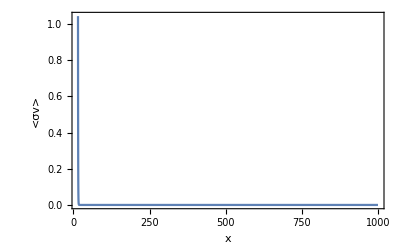

```mathematica
Plot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedNR[x]]} ,{x,15,1000},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"}]
```

```mathematica
Plot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedNRAnalyticalFunc[x]]} ,{x,15,1000},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"}]
```

$Aborted